## Differential equations, numerical solutions and visualisation

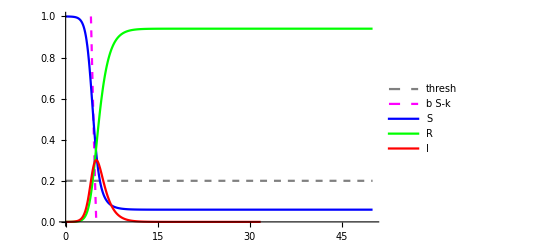

```mathematica
(* parameters *)
b=3;
k=1; (* recovery rate =  1/ expected duration til 'recovery' *)
threshold=0.2; (* representing e.g. saturation of health care facilities *)

(* x = susceptible, y= infectious, z= removed *)
X[x_, y_, z_]=- b x y ;
Y[x_, y_, z_]= b x y -k y ;
Z[x_, y_, z_]= k y ;
(* time & initial conditions *)
tmin=0; tmax=50;
s0=0.9999; i0=1-s0; r0=0;

(* numerical solution *)
ivp1={x'[t]==X[x[t],y[t],z[t]],y'[t]==Y[x[t],y[t],z[t]], z'[t]==Z[x[t],y[t],z[t]],x[0]==s0, y[0]==i0,z[0]==r0};
solveivp1[t_]={x[t],y[t],z[t]}/. NDSolve[ivp1,{x[t],y[t],z[t]},{t,tmin,tmax}];

(* plots *)
Plot[{threshold, b solveivp1[t][[1,1]] - k,solveivp1[t][[1,1]], solveivp1[t][[1,3]], solveivp1[t][[1,2]]},{t,tmin,tmax},PlotLegends->{"thresh", "b S-k","S", "R", "I"}, PlotStyle->{{RGBColor[0.5,0.5,0.5],Dashed}, {RGBColor[1,0,1],Dashed},RGBColor[0,0,1],RGBColor[0,1,0],{RGBColor[1,0,0],Thick}},PlotRange->{{tmin,tmax},{0,1}}]
```

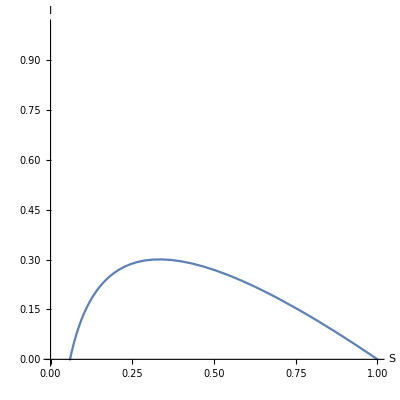

```mathematica
(* SI Phase Plane *)
ParametricPlot[{solveivp1[t][[1,1]], solveivp1[t][[1,2]]},{t,tmin,tmax}, PlotRange->{{0,1},{0,1}},AxesLabel->{"S","I"}]
```

## Interactive visualisations

```mathematica
Clear[b,k,i0];
(* x = susceptible, y= infectious, z= removed *)
X[x_, y_, z_]=- b x y ;
Y[x_, y_, z_]= b x y -k y ;
Z[x_, y_, z_]= k y ;

tmin=0; tmax=50;

ivppar={x'[t]==X[x[t],y[t],z[t]],y'[t]==Y[x[t],y[t],z[t]], z'[t]==Z[x[t],y[t],z[t]],x[0]==1-i0, y[0]==i0,z[0]==0};

ivpparsol=ParametricNDSolveValue[ivppar,{x[t],y[t],z[t]},{t,tmin,tmax},{k,b,i0}];

Manipulate[Plot[{ivpparsol[k0,b0,i0][[1]],ivpparsol[k0,b0,i0][[3]],ivpparsol[k0,b0,i0][[2]]},{t,tmin,tmax},PlotRange->{{tmin,tmax},{0,1}},PlotStyle->{RGBColor[0,0,1],RGBColor[0,1,0],{RGBColor[1,0,0],Thick}}], {{i0,.001},0,0.001},{{b0,1.5},1,3},{k0,1,3}]
```